## Some Basic Sound Calculations

```mathematica
speedOfSoundMetersPerSec = 343
```

343

```mathematica
cochleaDuctLengthMeters = 30*10^-3
```

3/100

```mathematica
humanHearingRageHz = {20, 20000}
```

{20,20000}

```mathematica
humanHearingRangeSecondsPerCycle = {1.0/humanHearingRageHz[[2]], 1.0/humanHearingRageHz[[1]]}
```

{0.00005,0.05}

```mathematica
zeroDbSplPascals = 20×10^-6
```

1/50000

```mathematica
hearingRangePascals = {zeroDbSplPascals, 20}
```

{1/50000,20}

```mathematica
DBSPL[preasure] = 20×Log[10, preasure/zeroDbSpl]
```

(20 Log[preasure/zeroDbSpl])/Log[10]

```mathematica
humanAmplitudeMaxResolutionDbSpl  = 0.4
```

0.4

```mathematica
samplesRequiredPerWave = 8
```

8

```mathematica
MaxSourceTimeResolutionSeconds[sampleRate_] := samplesRequiredPerWave/sampleRate
```

```mathematica
MinSourceTimeResolutionSeconds = humanHearingRangeSecondsPerCycle[[2]]
```

0.05

## Import the Sound

```mathematica
utt354 =Import["/home/god/workspace/sdr-work/recordings/audio/3_5_4.wav",  "Data"]
```

{{0.0110172,0.00735496,0.00512711,0.00564592,0.00457778,0.000183111,0.00784326,0.00271615,0.00357067,0.005768,0.00231941,0.000122074,0.00790429,0.00204474,0.0069277,0.0158086,0.00448622,0.00900296,0.00686666,0.00283822,0.0109867,0.0120548,0.00335704,0.010651,0.00790429,0.00381481,0.0127567,0.0110477,0.0044557,0.00540178,0.00234993,0.00241096,0.00833155,0.00933866,0.000457778,0.00549333,-0.00180054,0.0112613,0.00354015,0.00167852,0.00888089,0.00451674,0.00210578,0.00146489,0.00167852,-0.0000915527,0.0151372,0.00717185,0.00711081,0.0138859,0.00402844,0.00320444,0.00689718,0.00326548,0.0101016,0.009888,0.00543229,0.00927763,0.00985748,0.00405896,0.0089114,0.00744652,0.00225837,0.00521867,0.00265511,0.00802637,0.01236,0.00341807,0.00668355,0.00762963,0.00518815,0.00704978,0.0100101,0.00436415,0.0112003,0.0013123,0.00225837,0.0125736,-0.00180054,-0.0020752,-0.000244141,-0.000793457,-0.00146484,-0.00164795,0.00463881,0.00927763,0.00259407,0.007416,0.0115055,0.0019837,0.0036317,0.00354015,0.00253304,0.0103458,0.00878933,0.007416,0.004944,0.00155644,0.00360118,0.00466933,0.00473037,-0.00109863,0.00732444,0.00338755,0.00274667,0.0110477,0.0061037,0.00570696,0.00845363,0.00967437,0.00344859,0.005768,0.00662252,0.00424207,0.0107425,0.00863674,0.00982696,0.00674459,0.00412,0.00592059,0.00781274,0.00225837,0.00616474,0.00723289,0.00430311,0.00427259,0.001648,0.00582904,0.00476089,0.00646992,0.00265511,0.00323496,0.0011597,0.00354015,0.0102237,220230,0.0141301,0.0180364,0.0238655,0.0170293,0.0179449,0.0190435,0.0121464,0.0195929,0.0208747,0.019837,0.0138554,0.0210578,0.015717,0.012421,0.0281686,0.0183721,0.0187994,0.0242622,0.0149846,0.0159001,0.0243843,0.0248726,0.0189215,0.0219428,0.0198981,0.0102237,0.0162664,0.0267342,0.0217597,0.0224616,0.0260933,0.0261238,0.0216987,0.0226447,0.018189,0.0193793,0.0198675,0.0178533,0.0108951,0.0212104,0.0199286,0.0183111,0.0220649,0.0196844,0.0153508,0.0205695,0.0212104,0.018128,0.0265816,0.0216071,0.0183111,0.0259102,0.0202033,0.0191351,0.0224006,0.0125126,0.0153203,0.0202338,0.0114444,0.0135197,0.0164495,0.0171209,0.0128788,0.0238044,0.0219428,0.0143742,0.0209662,0.0178533,0.0122074,0.0130924,0.0117496,0.0128483,0.0137028,0.0149236,0.0162053,0.0245369,0.0182806,0.0198065,0.0218207,0.018067,0.0180059,0.018067,0.0194403,0.0232246,0.0164495,0.0223395,0.0159307,0.0227058,0.0204169,0.0141301,0.0227058,0.0208747,0.0209052,0.0263985,0.0275582,0.0231635,0.0310678,0.0195624,0.017304,0.0302438,0.0234077,0.0228584,0.023072,0.0186163,0.0136418,0.0219733,0.0208441,0.0118412,0.0228584,0.0191961,0.0151982,0.025605,0.0219428,0.00955229,0.0138859,0.018128,0.0119938,0.0155339,0.0135807,0.0176702,0.022309,0.0174566,0.00836207,0.0169073,0.0151677,0.0120243,0.0193487,0.0172124,0.0162358,0.0202033,0.0184942,0.018952,0.016419,0.0195624,0.0195624},{1}}
 |  |  |  |

```mathematica
{Min[utt354[[1]]], Max[utt354[[1]]]}
```

{-0.483337,0.549242}

```mathematica
uttSampleRate = 44100
```

44100

```mathematica
sourceSignalRangeSecondsPerCycle = {MaxSourceTimeResolutionSeconds[uttSampleRate]×1.0, MinSourceTimeResolutionSeconds}
```

{0.000181406,0.05}

## Formula for the number of samples in a given time window

```mathematica
SamplesPerWindow[windowSizeSeconds_, sampleRate_] := Round[windowSizeSeconds × sampleRate]
```

## Formular to partition data at a given time resolution and overlap

```mathematica
PartitionSampleData[data_, requiredTimeResolution_, requiredTimeOverlap_] := Partition[data, 
SamplesPerWindow[requiredTimeResolution, uttSampleRate], 
Round[SamplesPerWindow[requiredTimeResolution, uttSampleRate]-SamplesPerWindow[requiredTimeOverlap, uttSampleRate]]]
```

```mathematica
PartitionSampleData[utt354[[1]], 0.0001, 0]
```

{{0.0110172,0.00735496,0.00512711,0.00564592},{0.00457778,0.000183111,0.00784326,0.00271615},55122,{0.018952,0.016419,0.0195624,0.0195624}}
 |  |  |  |

## Compute freq of deltas in partition

Deltas are with respect to the sample at the center of the window and can thus be negative or positive

```mathematica
values = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
Length[values]
```

```mathematica
values[[3]]
```

3

```mathematica
WindowDelta[values_] := Table[values[[Ceiling[Length[values]/2]]] - values[[i]], {i,1,Length[values]}]
```

```mathematica
WindowDelta[{1,2,3,4,5}]
```

{2,1,0,-1,-2}

```mathematica
deltas = Map[WindowDelta , partitionedData]
```

{{-0.00891113,0.00280762,0.000976563,0.000762939,0.0050354,-0.00717163,-0.00531006,427,-0.0101013,-0.0153503,-0.0104065,-0.00268555,-0.00796509,-0.000488281,-0.006073},524,{1}}
 |  |  |  |

```mathematica
Length[deltas]
```

526

```mathematica
Length[deltas[[1]]]
```

441

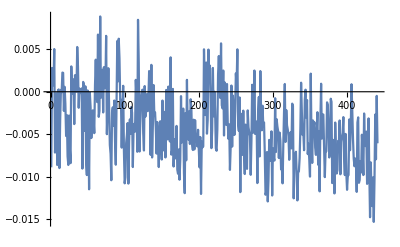

```mathematica
ListLinePlot[deltas[[1]]]
```

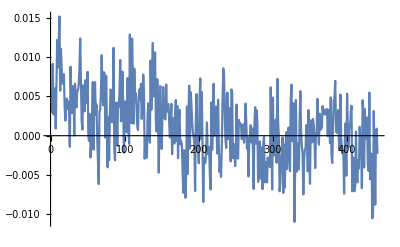

```mathematica
ListLinePlot[deltas[[400]]]
```

```mathematica
ListSeriesDelta[twosome_] := Table[twosome[[2,i]]-twosome[[1,i]], {i, 1, Length[twosome[[1]]]}]
```

```mathematica
test = {{1,2,3,4,5},{3,4,5,6,7}}
```

{{1,2,3,4,5},{3,4,5,6,7}}
 |  |  |  |

```mathematica
test[[1,1]]
```

1

```mathematica
ListSeriesDelta[test]
```

{2,2,2,2,2}

```mathematica
partitionedData2 := Partition[partitionedData, 2]
```

```mathematica
ListSeriesDelta[partitionedData2[[1]]]
```

{-0.00384521,0.0098877,0.0108032,0.00332642,0.011261,-0.000762939,-0.000610352,0.0106812,425,0.000793457,-0.00848389,-0.0103455,-0.00247192,-0.00384521,-0.00317383,0.00674438,-0.000335693}
 |  |  |  |

```mathematica
Length[partitionedData2[[1,1]]]
```

441

```mathematica
partitionedData3 := Partition[Map[ListSeriesDelta, partitionedData2], 2]
```

```mathematica
partitionedData4 := Partition[Map[ListSeriesDelta, partitionedData3], 2]
```

```mathematica
partitionedData5 := Partition[Map[ListSeriesDelta, partitionedData4], 2]
```

```mathematica
partitionedData6 := Partition[Map[ListSeriesDelta, partitionedData5], 2]
```

```mathematica
partitionedData7 := Partition[Map[ListSeriesDelta, partitionedData6], 2]
```

```mathematica
partitionedData8 := Partition[Map[ListSeriesDelta, partitionedData7], 2]
```

```mathematica
partitionedData9 := Partition[Map[ListSeriesDelta, partitionedData8], 2]
```

```mathematica
partitionedData10 := Partition[Map[ListSeriesDelta, partitionedData9], 2]
```

```mathematica
partitionedData11 := Partition[Map[ListSeriesDelta, partitionedData10], 2]
```

```mathematica
partitionedData12 := Partition[Map[ListSeriesDelta, partitionedData11], 2]
```

```mathematica
Length[Flatten[partitionedData10]]
```

882

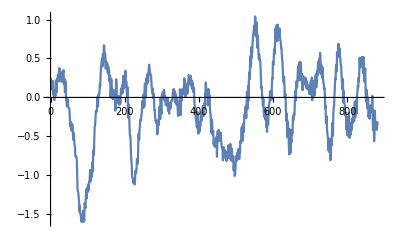

```mathematica
ListLinePlot[Flatten[partitionedData10]]
```

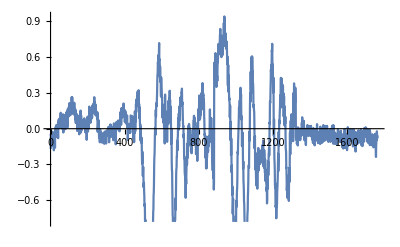

```mathematica
ListLinePlot[Flatten[partitionedData9]]
```

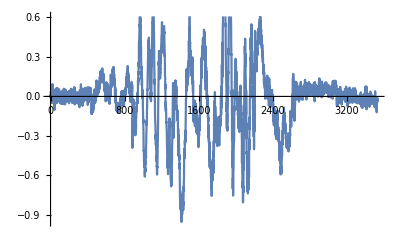

```mathematica
ListLinePlot[Flatten[partitionedData8]]
```

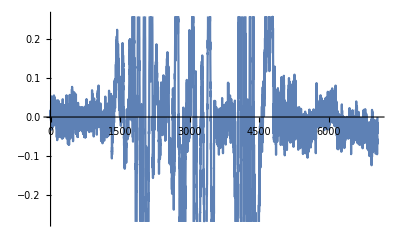

```mathematica
ListLinePlot[Flatten[partitionedData7]]
```

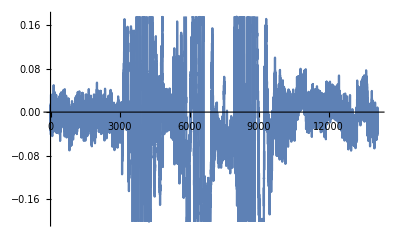

```mathematica
ListLinePlot[Flatten[partitionedData6]]
```

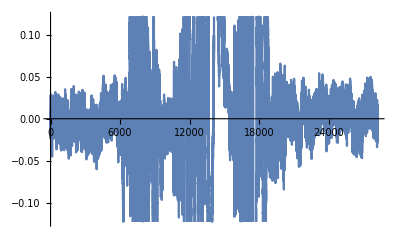

```mathematica
ListLinePlot[Flatten[partitionedData5]]
```

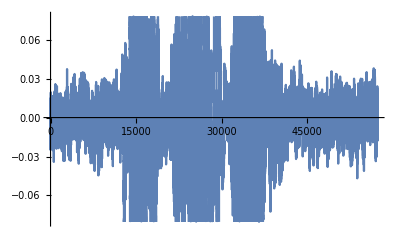

```mathematica
ListLinePlot[Flatten[partitionedData4]]
```

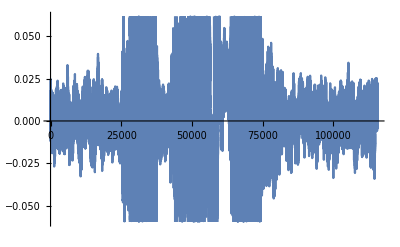

```mathematica
ListLinePlot[Flatten[partitionedData3]]
```

```mathematica
ListLinePlot[Flatten[partitionedData]]
```

-Graphics-

## Compose the delta function and the partition function to obtain a function that reduces the data

```mathematica
ReducePartitionedData =  Map[ListSeriesDelta, #]& @ Partition[#,2]&
```

(ListSeriesDelta/@#1&)[Partition[#1,2]]&
 |  |  |  |

```mathematica
resStandard = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], uttSampleWindowSize, windowStartInterval]
```

{{-0.794464,-0.760498,-0.67749,-0.711365,-0.770905,-0.720276,-0.608765,-0.834991,425,0.282867,-0.048645,-0.0264893,0.162933,0.105377,0.0159912,0.219391,0.261047}}
 |  |  |  |

```mathematica
res8 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 8, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911}}
 |  |  |  |

```mathematica
res50 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 50, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911,34,0.234589,0.217957,0.542175,0.198334,0.937714,0.432068,0.763092,-0.265381}}
 |  |  |  |

```mathematica
res250 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 2]
```

{{0.583221,-2.35056,-1.74783,1.46643,0.556976,-0.766968,0.643372,0.327911,234,-0.327484,0.0410156,-1.35034,-1.5495,0.704315,0.749481,0.169678,2.33649}}
 |  |  |  |

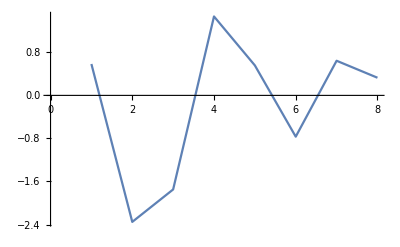
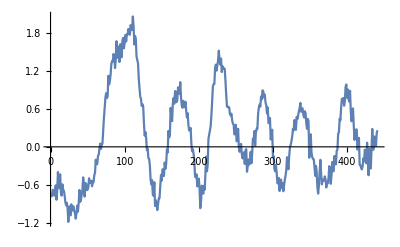
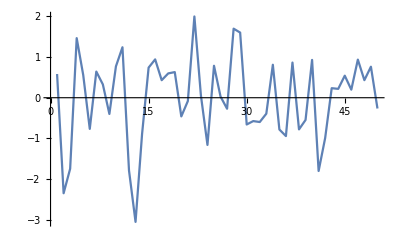
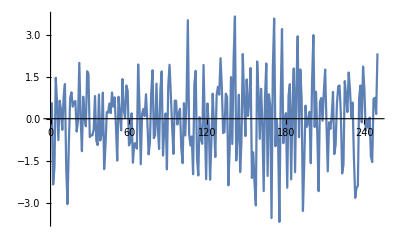

```mathematica
Map[ListLinePlot[#]&, {res8[[1]], resStandard, res50[[1]], res250[[1]]}]
```

```mathematica
res250020 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 20]
```

{{-3.72131,-3.21304,-2.77704,-3.23755,-2.75089,-2.7135,-3.38574,-2.75873,234,0.709503,0.291077,0.785889,0.771484,0.399597,0.799896,1.04684,0.208038}}
 |  |  |  |

```mathematica
res250040 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 40]
```

{{3.46735,2.86606,2.51257,2.52829,1.90601,1.72922,1.81238,1.47495,234,1.55817,1.89816,1.13342,0.803406,1.46494,0.970551,0.618042,1.45587}}
 |  |  |  |

```mathematica
res250060 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 60]
```

{{2.49695,2.75525,2.12292,2.06848,2.56219,2.5141,2.30844,2.56985,234,1.38733,1.43829,1.37448,1.22205,1.3754,1.28381,1.53201,1.31326}}
 |  |  |  |

```mathematica
res250010 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 10]
```

{{1.18793,0.954651,1.53387,0.719208,0.0709534,1.90866,2.11935,0.592621,234,-2.09143,-1.35547,-3.4093,-3.5076,-1.82779,-3.24225,-4.92456,-3.91388}}
 |  |  |  |

```mathematica
res25000 = NestWhile[ReducePartitionedData , #, Length[#]>1&] & @ Partition[utt135[[1,1,1]], 250, 1]
```

{{-2.93378,0.602722,3.21426,-0.909454,-1.32394,1.41034,-0.31546,-0.727295,234,0.3685,-1.39136,-0.199158,2.25381,0.045166,-0.579803,2.16681,0.449463}}
 |  |  |  |

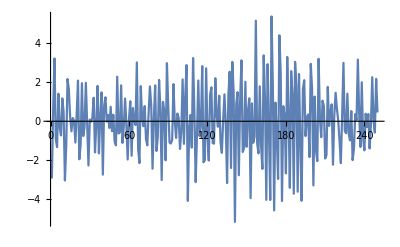
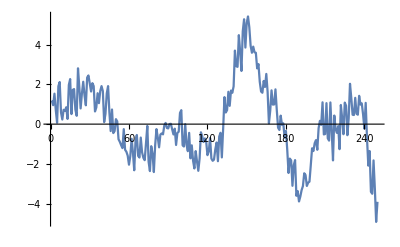
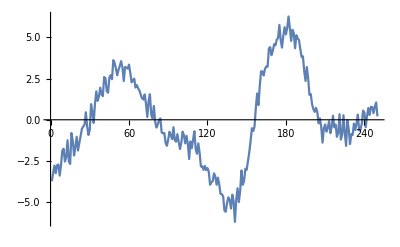
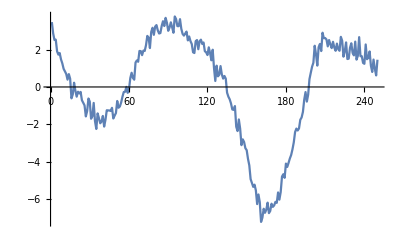
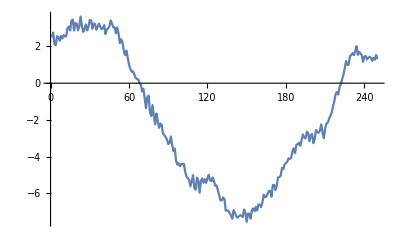
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListLinePlot[#]&, {res25000[[1]], res250[[1]], res250010[[1]], res250020[[1]], res250040[[1]], res250060[[1]]}]
```

## Determine deltas of deltas and any new deltas within resolution

use delta time resolution to filter deltas
deltass should be wrt middle